```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/412nm.dat"]
```

{{1.46129,-0.244469},{1.36603,-0.160439},{1.32759,-0.135087},{1.2815,-0.12314},{1.23231,-0.112228},{1.21009,-0.0932782},{1.18279,-0.132663},{1.15809,-0.242964},{1.13892,-0.351048},{1.12738,-0.393087},{1.09219,-0.280865},{1.09146,-0.16065},{1.09503,-0.0211113},{1.10053,-0.000220024},{1.1079,-0.00181164},{1.12128,0.00558438},{1.13179,-0.0496841},{1.14273,-0.0110306},{1.16583,-0.0357308},{1.1846,-0.0304283},{1.20387,-0.0203558},{1.22314,-0.0488227},{1.24682,-0.0531793}}

0.0758668-0.162144 x

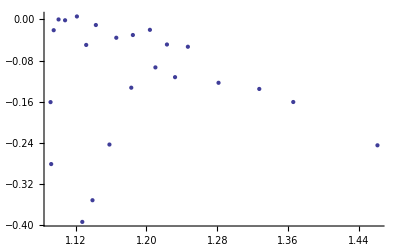

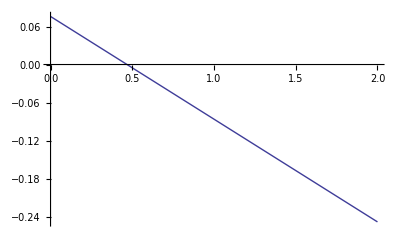

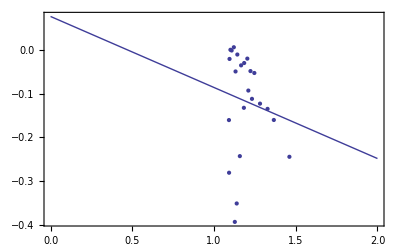

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```